```mathematica
Clear["Global`*"]
(* Probabilities that the donor is good given observations. Oij is the probability that the donor is good given the observation of a recipient doing action i={c,d}={cooperate,defect} to a recipient with reputation j={g,b}={good,bad}. Specifically, Ocg=P(good|->G), Ocb=P(good|->B), Odg=P(good|¬->G), and Odb=P(good|¬->B). *)
Pcg=ϵ*ghat/(ϵ*ghat+e*(1-ghat));
Pcb=Pcg;
Pdg=(1-ϵ)*ghat/((1-ϵ)*ghat+(1-e)*(1-ghat));
Pdb=Pdg;
(* Probabilities that a donor is good given their intention. Iij is the probability that the donor is good given their intention i={c,d}={cooperate,defect} to a recipient with reputation j={g,b}={good,bad}. *)
Qcg= ϵ*Pcg + (1-ϵ)*Pdg;
Qcb= Qcg;
Qdg= (1-e)*Pdg + e*Pcg;
Qdb= Qdg;
```

```mathematica
FullSimplify[Solve[g-Qcg*x-Qdg*y-(1-x-y)*(Qcg*g+Qdg*(1-g))==0,g]]
```

{{g→(ghat (e (-1+ghat) (1+e (-1+x))-(ghat+2 e (-1+ghat) x) ϵ+(ghat+(-1+ghat) x) ϵ^2))/(e (-1+ghat) (1+e (-1+ghat (x+y)))+ghat (-1-2 e (-1+ghat) (x+y)) ϵ+ghat (1+(-1+ghat) x+(-1+ghat) y) ϵ^2)}}

```mathematica
(* Changes in reputations for gx, gy, and gz *)
gxplus=(1-gx)*Icg/.{g-> x*gx+y*gy+z*gz};
gxminus=gx*(1-Icg)/.{g-> x*gx+y*gy+z*gz};
gyplus=(1-gy)*Idg/.{g-> x*gx+y*gy+z*gz};
gyminus=gy*(1-Idg)/.{g-> x*gx+y*gy+z*gz};
gzplus=(1-gz)*(Icg*(x*gx+y*gy+z*gz)+Idg*(x*(1-gx)+y*(1-gy)+z*(1-gz)))/.{g-> x*gx+y*gy+z*gz};
gzminus=gz*((1-Icg)*(x*gx+y*gy+z*gz)+(1-Idg)*(x*(1-gx)+y*(1-gy)+z*(1-gz)))/.{g-> x*gx+y*gy+z*gz};
Δgx=gxplus-gxminus/.{x->x[t],y->y[t],z->z[t],gx->gx[t],gy->gy[t],gz->gz[t]};
Δgy=gyplus-gyminus/.{x->x[t],y->y[t],z->z[t],gx->gx[t],gy->gy[t],gz->gz[t]};
Δgz=gzplus-gzminus/.{x->x[t],y->y[t],z->z[t],gx->gx[t],gy->gy[t],gz->gz[t]};
(*Solve[gxplus==gxminus&&gyplus==gyminus&&gzplus==gzminus,{gx,gy,gz}]*)
(*{{Gx,Gy,Gz}}=Values[Solve[gxplus==gxminus&&gyplus==gyminus&&gzplus==gzminus,{gx,gy,gz}]]/.{x->x[t],y->y[t],z->z[t]}*)
```

```mathematica
(* The replicator equations *)
Px=r*(x[t]+z[t]*gx[t])-1;
Py=r*(x[t]+z[t]*gy[t]);
Pz=r*(x[t]+z[t]*gz[t])-x[t]*gx[t]-y[t]*gy[t]-z[t]*gz[t];
Pbar=x[t]*Px+y[t]*Py+z[t]*Pz;
xdot=x[t]*(Px-Pbar);
ydot=y[t]*(Py-Pbar);
zdot=z[t]*(Pz-Pbar);
```

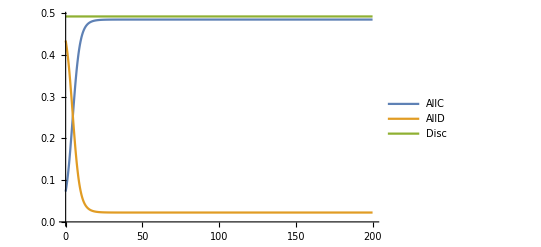

```mathematica
(* Plot numerical solutions *)
params={τ-> 100000,r->3,ϵ->(1-e1)*(1-e2)+e1*e2,e->e2,e1->0.01,e2->0.01};
eqns={x'[t]==xdot,y'[t]==ydot,z'[t]==zdot,gx'[t]==τ*Δgx,gy'[t]==τ*Δgy,gz'[t]==τ*Δgz}//.params;
rand1=RandomReal[];
rand2=RandomReal[];
rand3=RandomReal[];
x0=rand1/(rand1+rand2+rand3);
y0=rand2/(rand1+rand2+rand3);
z0=rand3/(rand1+rand2+rand3);
gx0=RandomReal[];
gy0=RandomReal[];
gz0=RandomReal[];
IC={x[0]==x0,y[0]==y0,z[0]==z0,gx[0]==gx0,gy[0]==gy0,gz[0]== gz0};
sol=NDSolve[Join[eqns,IC],{x,y,z,gx,gy,gz},{t,0,200}];
Plot[Evaluate[{x[t],y[t],z[t]}/.sol],{t,0,200},PlotLegends->{"AllC","AllD","Disc"}]
```

```mathematica
nsoleq={0==xdot,0==ydot,0==zdot,0==Δgx,0==Δgy,0==Δgz};
conds={0≤ x≤ 1,0≤y≤ 1,0≤z≤ 1,x+y+z==1,0≤gx≤ 1,0≤gy≤ 1,0≤gz≤ 1}
nsol=NSolve[Join[nsoleq,conds]/.{x[t]->x,y[t]->y,z[t]->z,gx[t]->gx,gy[t]->gy,gz[t]->gz},{x,y,z,gx,gy,gz},Reals]
```

{0≤x≤1,0≤y≤1,0≤z≤1,x+y+z==1,0≤gx≤1,0≤gy≤1,0≤gz≤1}

$Aborted

```mathematica
Pc=ϵ*g/(ϵ*g+e*(1-g));
Pd=(1-ϵ)*g/((1-ϵ)*g+(1-e)*(1-g));
Qc=ϵ*Pc+(1-ϵ)*Pd;
Qd=(1-e)*Pd+e*Pc;
Solve[g==Qd*(1-z)+(Qc*g+Qd*(1-g))*z,g]
```

{{g→0},{g→0},{g→1}}

```mathematica
Simplify[Qd*(1-z)+(Qc*g+Qd*(1-g))*z-g]
```

((-1+g) g^2 (-1+z) (e-ϵ)^2)/((e (-1+g)-g ϵ) (1+e (-1+g)-g ϵ))

```mathematica
Simplify[Qc*g+Qd*(1-g)-g]
```

0

```mathematica
gz=gx*g+gy*(1-g);
Pix=r*(x+gx*z)-1;
Piy=r*(x+gy*z);
Piz=r*(x+gz*z)-g;
Pibar=x*Pix+y*Piy+(1-x-y)*Piz;
Simplify[Piz-X*Pix-Y*Piy-(1-X-Y)*Piz]
```

((-1+g) X+g Y) (-1+gx r z-gy r z)

```mathematica
Solve[g-X*gx-Y*gy-(1-X-Y)*gz==0,{g}]
```

{{g→(gy+gx X-gy X)/(1-gx+gy+gx X-gy X+gx Y-gy Y)}}

```mathematica
Solve[(1-Gz)*(Q*g+R*(1-g))==Gz*((1-Q)*g+(1-R)*(1-g)),Gz]
```

{{Gz→g Q+R-g R}}

```mathematica
Solve[(-1+g) X+g Y==0,g]
```

{{g→X/(X+Y)}}

```mathematica
FullSimplify[Qcg-g/.{g->x/(x+y)}]
```

-(x y^2 (e-ϵ)^2)/((x+y) ((-1+e) y+x (-1+ϵ)) (e y+x ϵ))

```mathematica
Solve[g==x*Qcg+y*Qdg+(1-x-y)*(g*Qcg+(1-g)*Qdg),g]
```

{{g→0},{g→1},{g→x/(x+y)}}

```mathematica
Solve[Piy-Pibar==0//.{gx->Qcg,gy->Qdg,g->x/(x+y),z->1-x-y},x]
```

{{x→0},{x→(e y-e^2 r y+e^2 r y^2+y ϵ-2 e y ϵ+2 e r y ϵ-2 e r y^2 ϵ-r y ϵ^2+r y^2 ϵ^2-√(-4 (-e y^2+e^2 y^2) (-e^2 r y-ϵ+2 e r y ϵ+ϵ^2-r y ϵ^2)+(-e y+e^2 r y-e^2 r y^2-y ϵ+2 e y ϵ-2 e r y ϵ+2 e r y^2 ϵ+r y ϵ^2-r y^2 ϵ^2)^2))/(2 (-e^2 r y-ϵ+2 e r y ϵ+ϵ^2-r y ϵ^2))},{x→(e y-e^2 r y+e^2 r y^2+y ϵ-2 e y ϵ+2 e r y ϵ-2 e r y^2 ϵ-r y ϵ^2+r y^2 ϵ^2+√(-4 (-e y^2+e^2 y^2) (-e^2 r y-ϵ+2 e r y ϵ+ϵ^2-r y ϵ^2)+(-e y+e^2 r y-e^2 r y^2-y ϵ+2 e y ϵ-2 e r y ϵ+2 e r y^2 ϵ+r y ϵ^2-r y^2 ϵ^2)^2))/(2 (-e^2 r y-ϵ+2 e r y ϵ+ϵ^2-r y ϵ^2))}}

```mathematica
Pidiff=FullSimplify[Pix-Piy//.{gx->Qcg,gy->Qdg,g->x/(x+y),z->1-x-y}]
```

(e^2 y (-y+r x (-1+x+y))+x ϵ (x+y+r (-1+y) y ϵ+x (-1+r y) ϵ)+e y (x+y-2 x (1+r (-1+x+y)) ϵ))/(((-1+e) y+x (-1+ϵ)) (e y+x ϵ))

```mathematica
MyDiff=FullSimplify[r*x(Qcg-Qdg)/(x+y)//.{g->x/(x+y)}]
TeXForm[MyDiff]
```

-(r x^2 y (e-ϵ)^2)/((x+y) ((-1+e) y+x (-1+ϵ)) (e y+x ϵ))

-\frac{r x^2 y (e-\epsilon )^2}{(x+y) ((e-1) y+x (\epsilon -1)) (e y+x \epsilon )}

```mathematica
mysol=Assuming[r>1&&1>ϵ>0.5>e>0&&1>g>0&&1>z>0,FullSimplify@Reduce[Pidiff==0]]
```

g+√((-1+g) (-1+g+4 g r z (-1+ϵ) ϵ))==1+2 (-1+g) (e+e g (-1+r z)+g (1-r z) ϵ)||1+2 (-1+g) (e+e g (-1+r z)+g (1-r z) ϵ)+√((-1+g) (-1+g+4 g r z (-1+ϵ) ϵ))==g

```mathematica
mysol/.{e->0.01,ϵ->0.9802}
```

y≠0

```mathematica
EqC=g+√((-1+g) (-1+g+4 g r z (-1+ϵ) ϵ))-1-2 (-1+g) (e+e g (-1+r z)+g (1-r z) ϵ)/.{g->x/(x+y),z->1-x-y}
```

-1+x/(x+y)-2 (-1+x/(x+y)) (e+(e x (-1+r (1-x-y)))/(x+y)+(x (1-r (1-x-y)) ϵ)/(x+y))+√((-1+x/(x+y)) (-1+x/(x+y)+(4 r x (1-x-y) (-1+ϵ) ϵ)/(x+y)))

```mathematica
Solve[EqC==0,y]
```

{{y→0},{y→(r x-r x^2)/(-1+r x)},{y→(-e x+e^2 r x-e^2 r x^2-x ϵ+2 e x ϵ-2 e r x ϵ+2 e r x^2 ϵ+r x ϵ^2-r x^2 ϵ^2-√(-4 (e-e^2+e^2 r x-2 e r x ϵ+r x ϵ^2) (x^2 ϵ-x^2 ϵ^2)+(e x-e^2 r x+e^2 r x^2+x ϵ-2 e x ϵ+2 e r x ϵ-2 e r x^2 ϵ-r x ϵ^2+r x^2 ϵ^2)^2))/(2 (e-e^2+e^2 r x-2 e r x ϵ+r x ϵ^2))},{y→(-e x+e^2 r x-e^2 r x^2-x ϵ+2 e x ϵ-2 e r x ϵ+2 e r x^2 ϵ+r x ϵ^2-r x^2 ϵ^2+√(-4 (e-e^2+e^2 r x-2 e r x ϵ+r x ϵ^2) (x^2 ϵ-x^2 ϵ^2)+(e x-e^2 r x+e^2 r x^2+x ϵ-2 e x ϵ+2 e r x ϵ-2 e r x^2 ϵ-r x ϵ^2+r x^2 ϵ^2)^2))/(2 (e-e^2+e^2 r x-2 e r x ϵ+r x ϵ^2))}}

```mathematica
mysols=Assuming[r>1&&1>ϵ>0.5>e>0&&1>x>0&&1>y>0&&1≥x+y,FullSimplify@Solve[EqC==0,x]]/.{e->0.01,ϵ->0.9802,r->3}
```

{{x→1/2 (1-y-√(1-(2 y)/3+y^2))},{x→1/2 (1-y+√(1-(2 y)/3+y^2))},{x→(y (1.85327-2.82386 y-0.9702 √((1+2.9406 (-1+y))^2-0.058812 (2+3 (-1+y)) (-1+y)-0.06 (1+y)+0.0003 (3 (-1+y)^2+4 y))))/(2 (0.9802-0.058512 y+0.960792 (-1+3 y)))},{x→(y (1.85327-2.82386 y+0.9702 √((1+2.9406 (-1+y))^2-0.058812 (2+3 (-1+y)) (-1+y)-0.06 (1+y)+0.0003 (3 (-1+y)^2+4 y))))/(2 (0.9802-0.058512 y+0.960792 (-1+3 y)))}}

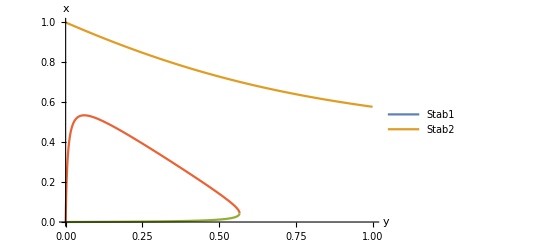

```mathematica
Plot[{x/.mysols[[1]],x/.mysols[[2]],x/.mysols[[3]],x/.mysols[[4]]},{y,0,1},PlotRange->{0,1},AxesLabel->{"y","x"},PlotLegends->{"Stab1","Stab2"}]
```

```mathematica
pix=r*(x+Qcg*(1-x-y))-1/.{g->x/(x+y)};
piy=r*(x+Qdg*(1-x-y))/.{g->x/(x+y)};
piz=r*(x+(g*Qcg+(1-g)*Qdg)*(1-x-y))-g/.{g->x/(x+y)};
pibar=x*pix+y*piy+(1-x-y)*piz;
```

```mathematica
J=Grad[{pix,piy},{x,y}]/.{e->0.01,ϵ->0.9802,r->3};
Stab1=Re[Eigenvalues[J]/.mysols[[3]]];
Stab2=Re[Eigenvalues[J]/.mysols[[4]]];
```

```mathematica
Plot[{Stab2},{y,0,1}]
```

```mathematica
1
```

```mathematica
Re[Stab2]/.{x->0.1}
```

{1/2 Re[(-(-4.50373×10^12 y^6+22)/(50. y+1)^2-√((1)^2/(1+1)^4-(2 y (1) (1))/((1) 1^4)))/((y+(y (1.85327-2.82386 y+0.9702 √(5+1)))/(2 (0.9802-0.058512 y+0.960792 (-1+3 y)))) (50. y+1)^2 (50. y+1/1)^2)],1/2 Re[(-1/1^2+√1)/((y+1/1) 1 1^2)]}
 |  |  |  |

```mathematica
mysols[[4]]/.{x->0.1}
```

{y→0.536208}

```mathematica
Stab2/.{x->0.38}
```

Stab2

```mathematica
MyDiff
```

MyDiff

```mathematica
Assuming[r>1&&1>ϵ>0.5>e>0&&1>x>0&&1>y>0&&1≥x+y,FullSimplify@Reduce[r*MyDiff>1]]
```

r>-((x+y) ((-1+e) y+x (-1+ϵ)) (e y+x ϵ))/(x^2 y (e-ϵ)^2)

```mathematica
FullSimplify[r*x^2 y (e-ϵ)^2+(x+y) ((-1+e) y+x (-1+ϵ)) (e y+x ϵ)]
```

r x^2 y (e-ϵ)^2+(x+y) ((-1+e) y+x (-1+ϵ)) (e y+x ϵ)

```mathematica
paraplot=Collect[r*x^2 y (e-ϵ)^2+(x+y) ((-1+e) y+x (-1+ϵ)) (e y+x ϵ),{x,y}]/.{e->0.01,ϵ->0.9802,r->3}
```

-0.019408 x^3+1.83386 x^2 y-0.980496 x y^2-0.0099 y^3

```mathematica
Mydiffs=MyDiff/.{e->0.01,ϵ->0.9802,r->3}
```

-(0.941288 x^2 y)/((-0.0198 x-0.99 y) (0.9802 x+0.01 y) (x+y))

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

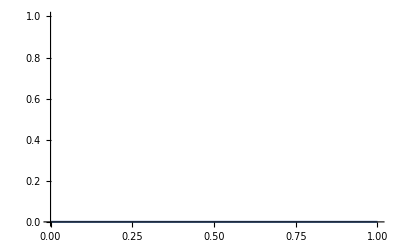

```mathematica
Plot[y/.Solve[Mydiffs==0,y],{x,0,1},PlotRange->{0,1}]
```

```mathematica
Simplify[MyDiff-1/.{x->y,ϵ->0.9802,e->0.01,r->3}]
```

0.412068

```mathematica
Jl=x/.mysols
```

{1/2 (1-y-√(1-(2 y)/3+y^2)),1/2 (1-y+√(1-(2 y)/3+y^2)),(y (1.85327-2.82386 y-0.9702 √((1+2.9406 (-1+y))^2-0.058812 (2+3 (-1+y)) (-1+y)-0.06 (1+y)+0.0003 (3 (-1+y)^2+4 y))))/(2 (0.9802-0.058512 y+0.960792 (-1+3 y))),(y (1.85327-2.82386 y+0.9702 √((1+2.9406 (-1+y))^2-0.058812 (2+3 (-1+y)) (-1+y)-0.06 (1+y)+0.0003 (3 (-1+y)^2+4 y))))/(2 (0.9802-0.058512 y+0.960792 (-1+3 y)))}

```mathematica
Solve[Jl[[4]]==0,y]
```

{{y→0.}}

```mathematica
myeq=Simplify[pix-piy]/.{x->y}
```

(e^2 y (-y+r y (-1+2 y))+e y (2 y-2 (1+r (-1+y)) y ϵ-2 r y^2 ϵ)+y ϵ (2 y+r (-1+y) y ϵ+y (-1+r y) ϵ))/(((-1+e) y+y (-1+ϵ)) (e y+y ϵ))

```mathematica
Solve[myeq==0,y]/.{e->0.01,ϵ->0.9802,r->3}
```

{{y→0.322955}}

```mathematica
Simplify[D[Qcg-g,g]/.{g->1}]
```

0

```mathematica
fx=Qcg-gx/.{g->x*gx+y*gy+(1-x-y)*gz};
fy=Qdg-gy/.{g->x*gx+y*gy+(1-x-y)*gz};
fz=Qcg*g+Qdg*(1-g)-gz/.{g->x*gx+y*gy+(1-x-y)*gz};
```

```mathematica
Simplify[Eigenvalues[Grad[{fx,fy,fz},{gx,gy,gz}]/.{gx->0,gy->0,gz->0}]]
Simplify[Eigenvalues[Grad[{fx,fy,fz},{gx,gy,gz}]//.{gx->Qcg,gy->Qdg,gz->Qcg*g+Qdg*(1-g),g->x/(x+y)}]]
Simplify[Eigenvalues[Grad[{fx,fy,fz},{gx,gy,gz}]/.{gx->1,gy->1,gz->1}]]
```

```mathematica
Simplify[Eigenvalues[Grad[{fx,fy,fz},{gx,gy,gz}]]/.{gx->Qcg,gy->Qdg,gz->Qcg*g+Qdg*(1-g)}]/.{g->x/(x+y)}
```

```mathematica
Simplify[{{{-1,-1,-1/((1)^2 (1)^2)(e-ϵ)^2 (e^10 (-1+1)^4 (1)^2 ((x^5 (-1+x/(x+y))^2)/(x+y)^2+(x y (-2+1/1^3+1+(x 1)/(x+y)))/(x+y)+(x^3 1 (-2-1+1))/(x+y)+x (1+(x^2 (6-8 y))/(x+y)^2+(2 x (-2+y))/(x+y)-(2 x^3 (2-5 y+y^2))/(x+y)^3+(x^4 (1-4 y+3 y^2))/(x+y)^4))+14+e^6 1^2 (1))}}, {{{, , , , }}}}]
```

{-1,-1,(x y (x+y) (e-ϵ)^2)/(((-1+e) y+x (-1+ϵ)) (e y+x ϵ))}

```mathematica
Simplify[Eigenvalues[Grad[{fx,fz}/.{y->0},{gx,gz}]/.{gx->0,gz->0}]]
```

{-1,-(x (e-ϵ)^2)/((-1+e) e)}

```mathematica
Simplify[Together[Qcg*g+Qdg*(1-g)-g]]
```

0

```mathematica
Simplify[Eigenvalues[Grad[{fy,fz}/.{x->0},{gy,gz}]/.{gy->1,gz->1}]]
```

{-(y (e-ϵ)^2)/((-1+ϵ) ϵ),-1}

```mathematica
Simplify[Together[r*(Qcg-Qdg)*z/.{g->x/(x+y),z->1-x-y}]]
```

(r x y (-1+x+y) (e-ϵ)^2)/(((-1+e) y+x (-1+ϵ)) (e y+x ϵ))

```mathematica
Simplify[x*(pix-pibar)]
```

(x y (e^2 y (-y+r x (-1+x+y))+e y (x+y-2 r x^2 ϵ-2 x (1+r (-1+y)) ϵ)+x ϵ (x+y+r (-1+y) y ϵ+x (-1+r y) ϵ)))/((x+y) ((-1+e) y+x (-1+ϵ)) (e y+x ϵ))

```mathematica
TeXForm[Simplify[x*(pix-pibar)]]
```

\frac{x y \left(e^2 y (r x (x+y-1)-y)+e y \left(-2 r x^2 \epsilon -2 x \epsilon  (r
   (y-1)+1)+x+y\right)+x \epsilon  (x \epsilon  (r y-1)+r (y-1) y \epsilon
   +x+y)\right)}{(x+y) ((e-1) y+x (\epsilon -1)) (e y+x \epsilon )}

```mathematica
x y (e^2 y (-y+r x (-1+x+y))+e y (x+y-2 r x^2 ϵ-2 x (1+r (-1+y)) ϵ)+x ϵ (x+y+r (-1+y) y ϵ+x (-1+r y) ϵ))
```

```mathematica
Collect[e^2 y (-y+r x (-1+x+y))+e y (x+y-2 r x^2 ϵ-2 x (1+r (-1+y)) ϵ)+x ϵ (x+y+r (-1+y) y ϵ+x (-1+r y) ϵ),r]
```

e x y+e y^2-e^2 y^2+x^2 ϵ+x y ϵ-2 e x y ϵ-x^2 ϵ^2+r (e^2 x y (-1+x+y)-2 e x^2 y ϵ-2 e x (-1+y) y ϵ+x^2 y ϵ^2+x (-1+y) y ϵ^2)

```mathematica
Clear["Global`*"]
```

```mathematica
FullSimplify[x*(pix-pibar)]
```

(x y (-1-(Qcg-Qdg) r (-1+x+y)))/(x+y)

```mathematica
Clear["Global`*"]
```

```mathematica
pix=r*(x+Qcg*z)-1;
piy=r*(x+Qdg*z);
piz=r*(x+(g*Qcg+(1-g)*Qdg)*z)-g;
pibar=x*pix+y*piy+z*piz;
FullSimplify[x*(pix-pibar)/.{g->x/(1-z),y->1-x-z}]
```

(x (-1+x+z) (-1+(Qcg-Qdg) r z))/(-1+z)

```mathematica
D[(Qcg-Qdg) r (-1+x+y)]
```

```mathematica
FullSimplify[D[Qcg-Qdg,g]]
```

-((e-ϵ)^2 ((-1+e) e (-1+g)^2+g^2 ϵ-g^2 ϵ^2))/((-1+e-e g+g ϵ)^2 (e-e g+g ϵ)^2)

```mathematica
Solve[(1-e) e (-1+g)^2-g^2 ϵ+g^2 ϵ^2==0,g]
```

{{g→(-e+e^2-√(e ϵ-e^2 ϵ-e ϵ^2+e^2 ϵ^2))/(-e+e^2+ϵ-ϵ^2)},{g→(-e+e^2+√(e ϵ-e^2 ϵ-e ϵ^2+e^2 ϵ^2))/(-e+e^2+ϵ-ϵ^2)}}

```mathematica
FullSimplify[Qcg-Qdg/.{g->x/(1-z)}]
```

(x (-1+x+z) (e-ϵ)^2)/((e (-1+x+z)-x ϵ) (1-z+e (-1+x+z)-x ϵ))

```mathematica
eqsol=FullSimplify[r*x (-1+x+z) (e-ϵ)^2-(e (-1+x+z)-x ϵ) (1-z+e (-1+x+z)-x ϵ)]
```

r x (-1+x+z) (e-ϵ)^2-(e (-1+x+z)-x ϵ) (1-z+e (-1+x+z)-x ϵ)

```mathematica
Collect[eqsol,{x,z}]
```

e-e^2+(-2 e+2 e^2) z+(e-e^2) z^2+x^2 (-e^2+r (e-ϵ)^2+2 e ϵ-ϵ^2)+x (-e+2 e^2-r (e-ϵ)^2+ϵ-2 e ϵ+z (e-2 e^2+r (e-ϵ)^2-ϵ+2 e ϵ))

```mathematica
eqsol2=FullSimplify[Qcg-Qdg/.{g->x/(1-z)}]
```

(x (-1+x+z) (e-ϵ)^2)/((e (-1+x+z)-x ϵ) (1-z+e (-1+x+z)-x ϵ))

```mathematica
eqsol2diff=FullSimplify[D[eqsol2,x]]
```

((-1+z) (e-ϵ)^2 ((-1+e) e (-1+x+z)^2+x^2 ϵ-x^2 ϵ^2))/((e (-1+x+z)-x ϵ)^2 (-1+z-e (-1+x+z)+x ϵ)^2)

```mathematica
Assuming[r>1&&1>ϵ>0.5>e>0&&1>x>0&&1>y>0&&1≥x+y,FullSimplify@Reduce[eqsol2diff<0]]
```

(e+ϵ<1&&((z<1&&(x+√(((-1+e) e (-1+z)^2 (-1+ϵ) ϵ)/((e-ϵ)^2 (-1+e+ϵ)^2))+((-1+e) e (-1+z))/((e-ϵ) (-1+e+ϵ))<0||-(e-e^2-e z+e^2 z-(e-ϵ) √(((-1+e) e (-1+z)^2 (-1+ϵ) ϵ)/((e-ϵ)^2 (-1+e+ϵ)^2)) (-1+e+ϵ))/((e-ϵ) (-1+e+ϵ))<x<((-1+e) (-1+z))/(-e+ϵ)||z+x ϵ>1+e (-1+x+z)))||(z>1&&(-(e-e^2-e z+e^2 z+(e-ϵ) √(((-1+e) e (-1+z)^2 (-1+ϵ) ϵ)/((e-ϵ)^2 (-1+e+ϵ)^2)) (-1+e+ϵ))/((e-ϵ) (-1+e+ϵ))<x<(e (-1+z))/(-e+ϵ)||(e (-1+z))/(-e+ϵ)<x<-(e-e^2-e z+e^2 z-(e-ϵ) √(((-1+e) e (-1+z)^2 (-1+ϵ) ϵ)/((e-ϵ)^2 (-1+e+ϵ)^2)) (-1+e+ϵ))/((e-ϵ) (-1+e+ϵ))))))||(e+ϵ==1&&((2 x+z>1&&((z>1&&x ϵ<e (-1+x+z))||(z+x ϵ<1+e (-1+x+z)&&z<1)))||(z<1&&z+x ϵ>1+e (-1+x+z))||(z>1&&x ϵ>e (-1+x+z))))||(e+ϵ>1&&((z<1&&((e (-1+e+z-e z)+√((-1+e) e (-1+z)^2 (-1+ϵ) ϵ))/((e-ϵ) (-1+e+ϵ))<x<((-1+e) (-1+z))/(-e+ϵ)||((-1+e) (-1+z))/(-e+ϵ)<x<(e (-1+e+z-e z)-√((-1+e) e (-1+z)^2 (-1+ϵ) ϵ))/((e-ϵ) (-1+e+ϵ))))||(z>1&&((-1+e+ϵ) (-(-1+e) e (-1+x+z)-x ϵ+x ϵ^2+√((-1+e) e (-1+z)^2 (-1+ϵ) ϵ))<0||(e (-1+e+z-e z)-√((-1+e) e (-1+z)^2 (-1+ϵ) ϵ))/((e-ϵ) (-1+e+ϵ))<x<(e (-1+z))/(-e+ϵ)||x ϵ>e (-1+x+z)))))

```mathematica
pix=r*(x+Qcg*(1-x-y))-1/.{g->x/(x+y)};
piy=r*(x+Qdg*(1-x-y))/.{g->x/(x+y)};
piz=r*(x+(g*Qcg+(1-g)*Qdg)*(1-x-y))-g/.{g->x/(x+y)};
pibar=x*pix+y*piy+(1-x-y)*piz;
fx=x*(pix-pibar);
Dfx=FullSimplify[D[fx,x]]
```

y^2 ((-1+r)/(x+y)^2-((-1+e)^2 r (-1+y))/(x ((-1+e) y+x (-1+ϵ)))+((-1+e)^3 r y (-1+x+y))/(x (x+y-e y-x ϵ)^2)-(e^3 r y (-1+x+y))/(x (e y+x ϵ)^2)+(e^2 r (-1+y))/(x (e y+x ϵ)))

```mathematica
Assuming[r>1&&1>ϵ>0.5>e>0&&1>x>0&&1>y>0&&1≥x+y,FullSimplify@Reduce[Dfx<0]]
```

$Aborted

```mathematica
FullSimplify[Dfx/.{y->x}]
```

1/4 (-1+(r (e-ϵ)^2 (e^2 (-3+8 x)+ϵ (-4 x+ϵ)+2 e (2-ϵ+x (-6+4 ϵ))))/((-2+e+ϵ)^2 (e+ϵ)^2))

```mathematica
Eqsol=FullSimplify[r*(Qcg-Qdg)*z-1/.{g->x/(1-z)}]
```

(e (-1+x+z) (-1+e+z-e z+e x (-1+r z))-x (-1+z+2 e (-1+x+z) (-1+r z)) ϵ+x (r (-1+z) z+x (-1+r z)) ϵ^2)/((e (-1+x+z)-x ϵ) (1-z+e (-1+x+z)-x ϵ))

```mathematica
DEqsol=FullSimplify[D[Eqsol,x]];
cond=FullSimplify[r*(Qcg-Qdg)*z-1/.{g->x/(1-z)}];
Assuming[r>1&&ϵ==(1-e)*(1-e1)+e*e1&&ϵ>0.5>e>0&&1>e1>0&&1>x>0&&1>z>0&&1≥x+z&&x==cond2,FullSimplify@Reduce[DEqsol<0]]
```

((-1+z) (-e+e^2+√((-1+e) e (-1+ϵ) ϵ)))/(e-e^2+(-1+ϵ) ϵ)<x<((-1+e) (-1+z))/(-e+ϵ)||e^2 (-1+x+z)+(1-z) √((-1+e) e (-1+ϵ) ϵ)<e (-1+x+z)+x (-1+ϵ) ϵ||z+x ϵ>1+e (-1+x+z)

```mathematica
{cond1,cond2}=Assuming[r>1&&ϵ==(1-e)*(1-e1)+e*e1&&ϵ>0.5>e>0&&1>e1>0&&1>x>0&&1>z>0&&1≥x+z&&cond==0,FullSimplify@Solve[Eqsol==0,x]]
```

{{x→-((-1+z) (1+e (-2+r z)-r z ϵ+√(1+r z (e (-2+e r z)-2 (1-2 e+e r z) ϵ+r z ϵ^2))))/(2 (-1+r z) (e-ϵ))},{x→((-1+z) (-1+e (2-r z)+r z ϵ+√(1+r z (e (-2+e r z)-2 (1-2 e+e r z) ϵ+r z ϵ^2))))/(2 (-1+r z) (e-ϵ))}}

```mathematica
test1=FullSimplify[DEqsol/.cond1];
test2=FullSimplify[DEqsol/.cond2];
Assuming[r>1&&ϵ==(1-e)*(1-e1)+e*e1&&ϵ>0.5>e>0&&1>e1>0&&z>conda&&1>z>0&&1>x>0,FullSimplify@Reduce[test1<0]]
```

r z<1||1/z<r<(e+ϵ-2 e ϵ-2 √((-1+e) e (-1+ϵ) ϵ))/(z (e-ϵ)^2)

```mathematica
test2
```

(8 r z (-1+r z)^2 (e-ϵ) (e^3 r^2 z^2+(-1+ϵ) (-1+r z ϵ) (-1+r z ϵ+√(1+r z (e (-2+e r z)-2 (1-2 e+e r z) ϵ+r z ϵ^2)))+e^2 r z (-2+4 ϵ-r z (1+ϵ)+√(1+r z (e (-2+e r z)-2 (1-2 e+e r z) ϵ+r z ϵ^2)))-e (-1+r^2 z^2 (-2+ϵ) ϵ+√(1+r z (e (-2+e r z)-2 (1-2 e+e r z) ϵ+r z ϵ^2))-2 ϵ √(1+r z (e (-2+e r z)-2 (1-2 e+e r z) ϵ+r z ϵ^2))+r z (-2-4 (-2+ϵ) ϵ+√(1+r z (e (-2+e r z)-2 (1-2 e+e r z) ϵ+r z ϵ^2))))))/((-1+z) (1+r z (-2+e+ϵ)+√(1+r z (e^2 r z+ϵ (-2+r z ϵ)-2 e (1-2 ϵ+r z ϵ))))^2 (-1+r z (e+ϵ)+√(1+r z (e^2 r z+ϵ (-2+r z ϵ)-2 e (1+(-2+r z) ϵ))))^2)

```mathematica
Together[r*(Qcg-Qdg)*z]
```

(r z (-e^2 g+e^2 g^2+2 e g ϵ-2 e g^2 ϵ-g ϵ^2+g^2 ϵ^2))/((-e+e g-g ϵ) (1-e+e g-g ϵ))

```mathematica
polyellipse=FullSimplify[r z (-e^2 g+e^2 g^2+2 e g ϵ-2 e g^2 ϵ-g ϵ^2+g^2 ϵ^2)-(-e+e g-g ϵ) (1-e+e g-g ϵ)/.{g->x/(1-z)}]
```

1/(-1+z)^2(e^2 (-1+x+z) (1-z+x (-1+r z))-e (-1+x+z) (1-z+2 x (-1+r z) ϵ)+x ϵ (1-x ϵ+z (-1+r (-1+x+z) ϵ)))

```mathematica
poly1=Collect[(e^2 (-1+x+z) (1-z+x (-1+r z))-e (-1+x+z) (1-z+2 x (-1+r z) ϵ)+x ϵ (1-x ϵ+z (-1+r (-1+x+z) ϵ))),x]
```

e-e^2-2 e z+2 e^2 z+e z^2-e^2 z^2+x^2 (e^2 (-1+r z)-2 e (-1+r z) ϵ-ϵ^2+r z ϵ^2)+x (-e+e^2+e z-e^2 z-e^2 (-1+r z)+e^2 z (-1+r z)+ϵ-z ϵ+2 e (-1+r z) ϵ-2 e z (-1+r z) ϵ-r z ϵ^2+r z^2 ϵ^2)

```mathematica
Solve[poly1==0,x]
```

{{x→(e-2 e^2-e z+2 e^2 z+e^2 r z-e^2 r z^2-ϵ+2 e ϵ+z ϵ-2 e z ϵ-2 e r z ϵ+2 e r z^2 ϵ+r z ϵ^2-r z^2 ϵ^2-(-1+z) (e-ϵ) √(1-2 e r z+e^2 r^2 z^2-2 r z ϵ+4 e r z ϵ-2 e r^2 z^2 ϵ+r^2 z^2 ϵ^2))/(2 (-e^2+e^2 r z+2 e ϵ-2 e r z ϵ-ϵ^2+r z ϵ^2))},{x→(e-2 e^2-e z+2 e^2 z+e^2 r z-e^2 r z^2-ϵ+2 e ϵ+z ϵ-2 e z ϵ-2 e r z ϵ+2 e r z^2 ϵ+r z ϵ^2-r z^2 ϵ^2+(-1+z) (e-ϵ) √(1-2 e r z+e^2 r^2 z^2-2 r z ϵ+4 e r z ϵ-2 e r^2 z^2 ϵ+r^2 z^2 ϵ^2))/(2 (-e^2+e^2 r z+2 e ϵ-2 e r z ϵ-ϵ^2+r z ϵ^2))}}

```mathematica
Solve[(e-2 e^2-e z+2 e^2 z+e^2 r z-e^2 r z^2-ϵ+2 e ϵ+z ϵ-2 e z ϵ-2 e r z ϵ+2 e r z^2 ϵ+r z ϵ^2-r z^2 ϵ^2+(-1+z) (e-ϵ) √(1-2 e r z+e^2 r^2 z^2-2 r z ϵ+4 e r z ϵ-2 e r^2 z^2 ϵ+r^2 z^2 ϵ^2))/(2 (-e^2+e^2 r z+2 e ϵ-2 e r z ϵ-ϵ^2+r z ϵ^2))==0,z]
```

{{z→1}}

```mathematica
plotter1=(e-2 e^2-e z+2 e^2 z+e^2 r z-e^2 r z^2-ϵ+2 e ϵ+z ϵ-2 e z ϵ-2 e r z ϵ+2 e r z^2 ϵ+r z ϵ^2-r z^2 ϵ^2-(-1+z) (e-ϵ) √(1-2 e r z+e^2 r^2 z^2-2 r z ϵ+4 e r z ϵ-2 e r^2 z^2 ϵ+r^2 z^2 ϵ^2))/(2 (-e^2+e^2 r z+2 e ϵ-2 e r z ϵ-ϵ^2+r z ϵ^2))/.{ϵ->0.9802,e->0.01,r->3};
plotter2=(e-2 e^2-e z+2 e^2 z+e^2 r z-e^2 r z^2-ϵ+2 e ϵ+z ϵ-2 e z ϵ-2 e r z ϵ+2 e r z^2 ϵ+r z ϵ^2-r z^2 ϵ^2+(-1+z) (e-ϵ) √(1-2 e r z+e^2 r^2 z^2-2 r z ϵ+4 e r z ϵ-2 e r^2 z^2 ϵ+r^2 z^2 ϵ^2))/(2 (-e^2+e^2 r z+2 e ϵ-2 e r z ϵ-ϵ^2+r z ϵ^2))/.{ϵ->0.9802,e->0.01,r->3};
```

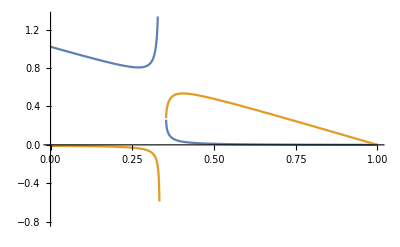

```mathematica
Plot[{plotter1,plotter2},{z,0,1}]
```

```mathematica
Solve[D[poly1,z]==0,z]
```

{{z→(2 e-2 e^2-e x+2 e^2 x+e^2 r x-e^2 r x^2+x ϵ-2 e x ϵ-2 e r x ϵ+2 e r x^2 ϵ+r x ϵ^2-r x^2 ϵ^2)/(2 (e-e^2+e^2 r x-2 e r x ϵ+r x ϵ^2))}}

```mathematica
cond3=FullSimplify[(2 e-2 e^2-e x+2 e^2 x+e^2 r x-e^2 r x^2+x ϵ-2 e x ϵ-2 e r x ϵ+2 e r x^2 ϵ+r x ϵ^2-r x^2 ϵ^2)/(2 (e-e^2+e^2 r x-2 e r x ϵ+r x ϵ^2))]
```

```mathematica
Solve[z==1/2 (1-x+(e+e^2 (-1+x)+x ϵ-2 e x ϵ)/(e+e^2 (-1+r x)-2 e r x ϵ+r x ϵ^2)),x]
```

{{x→1/(2 (e^2 r-2 e r ϵ+r ϵ^2))(-e+2 e^2+e^2 r-2 e^2 r z+ϵ-2 e ϵ-2 e r ϵ+4 e r z ϵ+r ϵ^2-2 r z ϵ^2-√(-4 (-2 e+2 e^2+2 e z-2 e^2 z) (e^2 r-2 e r ϵ+r ϵ^2)+(e-2 e^2-e^2 r+2 e^2 r z-ϵ+2 e ϵ+2 e r ϵ-4 e r z ϵ-r ϵ^2+2 r z ϵ^2)^2))},{x→1/(2 (e^2 r-2 e r ϵ+r ϵ^2))(-e+2 e^2+e^2 r-2 e^2 r z+ϵ-2 e ϵ-2 e r ϵ+4 e r z ϵ+r ϵ^2-2 r z ϵ^2+√(-4 (-2 e+2 e^2+2 e z-2 e^2 z) (e^2 r-2 e r ϵ+r ϵ^2)+(e-2 e^2-e^2 r+2 e^2 r z-ϵ+2 e ϵ+2 e r ϵ-4 e r z ϵ-r ϵ^2+2 r z ϵ^2)^2))}}

```mathematica
conda=1/(2 (e^2 r-2 e r ϵ+r ϵ^2))(-e+2 e^2+e^2 r-2 e^2 r z+ϵ-2 e ϵ-2 e r ϵ+4 e r z ϵ+r ϵ^2-2 r z ϵ^2-√(-4 (-2 e+2 e^2+2 e z-2 e^2 z) (e^2 r-2 e r ϵ+r ϵ^2)+(e-2 e^2-e^2 r+2 e^2 r z-ϵ+2 e ϵ+2 e r ϵ-4 e r z ϵ-r ϵ^2+2 r z ϵ^2)^2))
```

1/(2 (e^2 r-2 e r ϵ+r ϵ^2))(-e+2 e^2+e^2 r-2 e^2 r z+ϵ-2 e ϵ-2 e r ϵ+4 e r z ϵ+r ϵ^2-2 r z ϵ^2-√(-4 (-2 e+2 e^2+2 e z-2 e^2 z) (e^2 r-2 e r ϵ+r ϵ^2)+(e-2 e^2-e^2 r+2 e^2 r z-ϵ+2 e ϵ+2 e r ϵ-4 e r z ϵ-r ϵ^2+2 r z ϵ^2)^2))

```mathematica
FullSimplify[D[Qcg-Qdg/.{g->x/(1-z)},x]]
```

((-1+z) (e-ϵ)^2 ((-1+e) e (-1+x+z)^2+x^2 ϵ-x^2 ϵ^2))/((e (-1+x+z)-x ϵ)^2 (-1+z-e (-1+x+z)+x ϵ)^2)

```mathematica
FullSimplify[Qcg-Qdg/.{g->x/(1-z)}]
```

(x (-1+x+z) (e-ϵ)^2)/((e (-1+x+z)-x ϵ) (1-z+e (-1+x+z)-x ϵ))

```mathematica
((-1+e) e (-1+x+z)^2+x^2 ϵ-x^2 ϵ^2)
```

```mathematica
Assuming[r>1&&ϵ==(1-e)*(1-e1)+e*e1&&ϵ>0.5>e>0&&1>e1>0&&(Qcg-Qdg)>1&&1>z>0&&1>x>0,FullSimplify@Reduce[-((-1+e) e (-1+x+z)^2+x^2 ϵ-x^2 ϵ^2)<0]]
```

(1+√(-((-1+z) (-1+2 x+z))/x^2)>2 ϵ&&(x+z≥1||2 x+z>1))||(2 x+z==1&&((√(-(-1+z) (-1+2 x+z))+2 x ϵ==x&&2 e+√(((-1+x+z)^2-4 x^2 ϵ+4 x^2 ϵ^2)/(-1+x+z)^2)≠1)||(√(-((-1+z) (-1+2 x+z))/x^2)+2 ϵ≠1&&(1+√(((-1+x+z)^2-4 x^2 ϵ+4 x^2 ϵ^2)/(-1+x+z)^2)<2 e||2 e+√(((-1+x+z)^2-4 x^2 ϵ+4 x^2 ϵ^2)/(-1+x+z)^2)<1))))||((x+z>1||(x+z<1&&2 x+z>1))&&(((x+√(-(-1+z) (-1+2 x+z))==2 x ϵ||√(-(-1+z) (-1+2 x+z))+2 x ϵ==x)&&2 e+√(((-1+x+z)^2-4 x^2 ϵ+4 x^2 ϵ^2)/(-1+x+z)^2)≠1)||((1+√(-((-1+z) (-1+2 x+z))/x^2)<2 ϵ||√(-((-1+z) (-1+2 x+z))/x^2)+2 ϵ<1)&&(1+√(((-1+x+z)^2-4 x^2 ϵ+4 x^2 ϵ^2)/(-1+x+z)^2)<2 e||2 e+√(((-1+x+z)^2-4 x^2 ϵ+4 x^2 ϵ^2)/(-1+x+z)^2)<1))))||(2 x+z<1&&(1+√(((-1+x+z)^2-4 x^2 ϵ+4 x^2 ϵ^2)/(-1+x+z)^2)<2 e||2 e+√(((-1+x+z)^2-4 x^2 ϵ+4 x^2 ϵ^2)/(-1+x+z)^2)<1))

```mathematica
F=-((-1+e) e (-1+x+z)^2+x^2 ϵ-x^2 ϵ^2)
```

-(-1+e) e (-1+x+z)^2-x^2 ϵ+x^2 ϵ^2

```mathematica
Collect[F,x]
```

(1-e) e-2 (1-e) e z+(1-e) e z^2+x (-2 (1-e) e+2 (1-e) e z)+x^2 ((1-e) e-ϵ+ϵ^2)

```mathematica
Solve[F==0,x]
```

{{x→1/(2 (e-e^2-ϵ+ϵ^2))(2 e-2 e^2-2 e z+2 e^2 z-√((-2 e+2 e^2+2 e z-2 e^2 z)^2-4 (e-e^2-2 e z+2 e^2 z+e z^2-e^2 z^2) (e-e^2-ϵ+ϵ^2)))},{x→1/(2 (e-e^2-ϵ+ϵ^2))(2 e-2 e^2-2 e z+2 e^2 z+√((-2 e+2 e^2+2 e z-2 e^2 z)^2-4 (e-e^2-2 e z+2 e^2 z+e z^2-e^2 z^2) (e-e^2-ϵ+ϵ^2)))}}

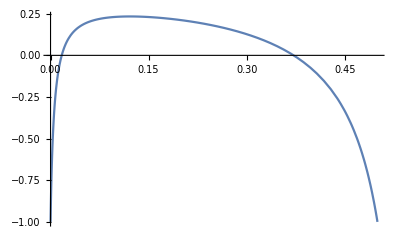

```mathematica
Plot[Evaluate[r*(Qcg-Qdg)*z-1//.{g->x/(1-z),z->0.5,e->0.01,r->3,ϵ->0.99*(1-0.1)+0.01*0.1}],{x,0,0.5}]
```

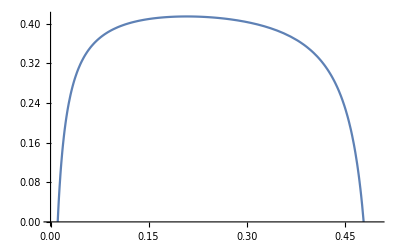

```mathematica
Plot[Evaluate[r*(Qcg-Qdg)*z-1//.{g->x/(1-z),z->0.5,e->0.01,r->3,ϵ->0.99*(1-0.01)+0.01*0.01}],{x,0,0.5}]
```

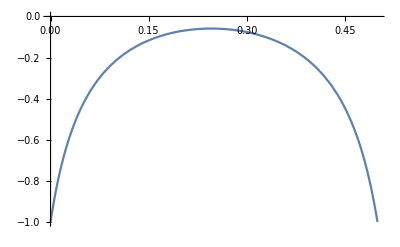

```mathematica
Plot[Evaluate[r*(Qcg-Qdg)*z-1//.{g->x/(1-z),z->0.5,e->0.1,r->3,ϵ->0.9*(1-0.01)+0.1*0.01}],{x,0,0.5}]
```

```mathematica
FullSimplify[D[F,x]]
```

-2 (-1+e) e (-1+x+z)-2 x ϵ+2 x ϵ^2

```mathematica
Together[r*(Qcg-Qdg)*z-1/.{g->x/(1-z)}]
```

(e-e^2-e x+2 e^2 x-e^2 x^2-2 e z+2 e^2 z+e x z-2 e^2 x z-e^2 r x z+e^2 r x^2 z+e z^2-e^2 z^2+e^2 r x z^2+x ϵ-2 e x ϵ+2 e x^2 ϵ-x z ϵ+2 e x z ϵ+2 e r x z ϵ-2 e r x^2 z ϵ-2 e r x z^2 ϵ-x^2 ϵ^2-r x z ϵ^2+r x^2 z ϵ^2+r x z^2 ϵ^2)/((-e+e x+e z-x ϵ) (1-e+e x-z+e z-x ϵ))

```mathematica
FullSimplify[(e-e^2-e x+2 e^2 x-e^2 x^2-2 e z+2 e^2 z+e x z-2 e^2 x z-e^2 r x z+e^2 r x^2 z+e z^2-e^2 z^2+e^2 r x z^2+x ϵ-2 e x ϵ+2 e x^2 ϵ-x z ϵ+2 e x z ϵ+2 e r x z ϵ-2 e r x^2 z ϵ-2 e r x z^2 ϵ-x^2 ϵ^2-r x z ϵ^2+r x^2 z ϵ^2+r x z^2 ϵ^2)]
```

```mathematica
mysol=Collect[e^2 (-1+x+z) (1-z+x (-1+r z))-e (-1+x+z) (1-z+2 x (-1+r z) ϵ)+x ϵ (1-x ϵ+z (-1+r (-1+x+z) ϵ)),x]
```

e-e^2-2 e z+2 e^2 z+e z^2-e^2 z^2+x^2 (e^2 (-1+r z)-2 e (-1+r z) ϵ-ϵ^2+r z ϵ^2)+x (-e+e^2+e z-e^2 z-e^2 (-1+r z)+e^2 z (-1+r z)+ϵ-z ϵ+2 e (-1+r z) ϵ-2 e z (-1+r z) ϵ-r z ϵ^2+r z^2 ϵ^2)

```mathematica
FullSimplify[e^2 (-1+r z)-2 e (-1+r z) ϵ-ϵ^2+r z ϵ^2]
```

(-1+r z) (e-ϵ)^2

```mathematica
Collect[FullSimplify[mysol/.{x->z}],z]
```

e-e^2+z (-3 e+4 e^2+ϵ-2 e ϵ)+z^3 (2 e^2 r-4 e r ϵ+2 r ϵ^2)+z^2 (2 e-4 e^2-e^2 r+4 e ϵ+2 e r ϵ-ϵ (1+ϵ+r ϵ))

```mathematica
Collect[e-e^2-2 e z+2 e^2 z+e z^2-e^2 z^2,z]
```

e-e^2+(-2 e+2 e^2) z+(e-e^2) z^2

```mathematica
FullSimplify[r*(Qcg-Qdg)-1/.{g->x/(1-z)}]
```

(e (-1+x+z) (-1+e+e (-1+r) x+z-e z)-x (-1+z+2 e (-1+r) (-1+x+z)) ϵ+x (-x+r (-1+x+z)) ϵ^2)/((e (-1+x+z)-x ϵ) (1-z+e (-1+x+z)-x ϵ))

```mathematica
top=Collect[-(e (-1+x+z) (-1+e+e (-1+r) x+z-e z)-x (-1+z+2 e (-1+r) (-1+x+z)) ϵ+x (-x+r (-1+x+z)) ϵ^2),x]
```

-e+e^2+2 e z-2 e^2 z-e z^2+e^2 z^2+x^2 (-e^2 (-1+r)+2 e (-1+r) ϵ+ϵ^2-r ϵ^2)+x (e-e^2+e^2 (-1+r)-e z+e^2 z-e^2 (-1+r) z-ϵ-2 e (-1+r) ϵ+z ϵ+2 e (-1+r) z ϵ+r ϵ^2-r z ϵ^2)

```mathematica
FullSimplify[e^2 (-1+r)-2 e (-1+r) ϵ-ϵ^2+r ϵ^2]
```

(-1+r) (e-ϵ)^2

```mathematica
FullSimplify[(-e+e^2-e^2 (-1+r)+e z-e^2 z+e^2 (-1+r) z+ϵ+2 e (-1+r) ϵ-z ϵ-2 e (-1+r) z ϵ-r ϵ^2+r z ϵ^2)]
```

(-1+z) (e-ϵ) (1+e (-2+r)-r ϵ)

```mathematica
FullSimplify[e-e^2-2 e z+2 e^2 z+e z^2-e^2 z]
```

e (-1+z) (-1+e+z)

```mathematica
FullSimplify[x*(pix-pibar)]
```

(x y (e^2 y (-y+r x (-1+x+y))+x ϵ (x+y+r (-1+y) y ϵ+x (-1+r y) ϵ)+e y (x+y-2 x (1+r (-1+x+y)) ϵ)))/((x+y) ((-1+e) y+x (-1+ϵ)) (e y+x ϵ))

```mathematica
FullSimplify[Solve[top==0,x]]
```

{{x→((-1+z) (-1-e (-2+r)+r ϵ+√((-1+e r)^2-2 (1+e (-2+r)) r ϵ+r^2 ϵ^2)))/(2 (-1+r) (e-ϵ))},{x→-((-1+z) (1+e (-2+r)-r ϵ+√((-1+e r)^2-2 (1+e (-2+r)) r ϵ+r^2 ϵ^2)))/(2 (-1+r) (e-ϵ))}}

```mathematica
top1=((-1+z) (-1-e (-2+r)+r ϵ+√((-1+e r)^2-2 (1+e (-2+r)) r ϵ+r^2 ϵ^2)))/(2 (-1+r) (e-ϵ));
Assuming[r>1&&1>ϵ>0.5>e>0&&1>z>0&&1>x>0,FullSimplify@Reduce[D[top1,ϵ]<0]]
```

e+ϵ<1&&r (e+ϵ-2 e ϵ+2 √((-1+e) e (-1+ϵ) ϵ))<1

```mathematica
FullSimplify[-1-2 e (-1+r)+z+2 e (-1+r) z+2 r ϵ-2 r z ϵ]
```

(-1+z) (1+2 e (-1+r)-2 r ϵ)

```mathematica
Solve[top==0,x]
```

{{x→(-e+2 e^2-e^2 r+e z-2 e^2 z+e^2 r z+ϵ-2 e ϵ+2 e r ϵ-z ϵ+2 e z ϵ-2 e r z ϵ-r ϵ^2+r z ϵ^2-(-1+z) (e-ϵ) √(1-2 e r+e^2 r^2-2 r ϵ+4 e r ϵ-2 e r^2 ϵ+r^2 ϵ^2))/(2 (e^2-e^2 r-2 e ϵ+2 e r ϵ+ϵ^2-r ϵ^2))},{x→(-e+2 e^2-e^2 r+e z-2 e^2 z+e^2 r z+ϵ-2 e ϵ+2 e r ϵ-z ϵ+2 e z ϵ-2 e r z ϵ-r ϵ^2+r z ϵ^2+(-1+z) (e-ϵ) √(1-2 e r+e^2 r^2-2 r ϵ+4 e r ϵ-2 e r^2 ϵ+r^2 ϵ^2))/(2 (e^2-e^2 r-2 e ϵ+2 e r ϵ+ϵ^2-r ϵ^2))}}

```mathematica
D[(-e+2 e^2-e^2 r+e z-2 e^2 z+e^2 r z+ϵ-2 e ϵ+2 e r ϵ-z ϵ+2 e z ϵ-2 e r z ϵ-r ϵ^2+r z ϵ^2-(-1+z) (e-ϵ) √(1-2 e r+e^2 r^2-2 r ϵ+4 e r ϵ-2 e r^2 ϵ+r^2 ϵ^2))/(2 (e^2-e^2 r-2 e ϵ+2 e r ϵ+ϵ^2-r ϵ^2)),ϵ]
```

(1-2 e+2 e r-z+2 e z-2 e r z-2 r ϵ+2 r z ϵ-((-1+z) (e-ϵ) (-2 r+4 e r-2 e r^2+2 r^2 ϵ))/(2 √(1-2 e r+e^2 r^2-2 r ϵ+4 e r ϵ-2 e r^2 ϵ+r^2 ϵ^2))+(-1+z) √(1-2 e r+e^2 r^2-2 r ϵ+4 e r ϵ-2 e r^2 ϵ+r^2 ϵ^2))/(2 (e^2-e^2 r-2 e ϵ+2 e r ϵ+ϵ^2-r ϵ^2))-((-2 e+2 e r+2 ϵ-2 r ϵ) (-e+2 e^2-e^2 r+e z-2 e^2 z+e^2 r z+ϵ-2 e ϵ+2 e r ϵ-z ϵ+2 e z ϵ-2 e r z ϵ-r ϵ^2+r z ϵ^2-(-1+z) (e-ϵ) √(1-2 e r+e^2 r^2-2 r ϵ+4 e r ϵ-2 e r^2 ϵ+r^2 ϵ^2)))/(2 (e^2-e^2 r-2 e ϵ+2 e r ϵ+ϵ^2-r ϵ^2)^2)